```mathematica
Tsingle=Inverse[{{1,1},{I k,-I k}}].{{1,1},{κ,-κ}}.{{E^(-κ a),0},{0,E^(κ a)}}.Inverse[{{1,1},{κ,-κ}}].{{1,1},{I k,-I k}}//FullSimplify
```

{{Cosh[a κ]+(ⅈ (-k+κ) (k+κ) Sinh[a κ])/(2 k κ),(ⅈ (k^2+κ^2) Sinh[a κ])/(2 k κ)},{-(ⅈ (k^2+κ^2) Sinh[a κ])/(2 k κ),Cosh[a κ]+(ⅈ (k-κ) (k+κ) Sinh[a κ])/(2 k κ)}}

```mathematica
Tdouble=Tsingle.{{E^(-I k b),0},{0,E^(I k b)}}.Tsingle//FullSimplify
```

{{(ⅇ^(ⅈ b k) (k^2+κ^2)^2 Sinh[a κ]^2+ⅇ^(-ⅈ b k) (2 k κ Cosh[a κ]-ⅈ (k-κ) (k+κ) Sinh[a κ])^2)/(4 k^2 κ^2),(-ⅈ (k^4-κ^4) Sin[b k] Sinh[a κ]^2+ⅈ k κ (k^2+κ^2) Cos[b k] Sinh[2 a κ])/(2 k^2 κ^2)},{(ⅈ ((k^4-κ^4) Sin[b k] Sinh[a κ]^2-k κ (k^2+κ^2) Cos[b k] Sinh[2 a κ]))/(2 k^2 κ^2),(ⅇ^(-ⅈ b k) (k^2+κ^2)^2 Sinh[a κ]^2+ⅇ^(ⅈ b k) (2 k κ Cosh[a κ]+ⅈ (k-κ) (k+κ) Sinh[a κ])^2)/(4 k^2 κ^2)}}

```mathematica
Ti=(ⅇ^(ⅈ b k) (k^2+κ^2)^2 Sinh[a κ]^2+ⅇ^(-ⅈ b k) (2 k κ Cosh[a κ]-ⅈ (k-κ) (k+κ) Sinh[a κ])^2)/(4 k^2 κ^2) (ⅇ^(-ⅈ b k) (k^2+κ^2)^2 Sinh[a κ]^2+ⅇ^(ⅈ b k) (2 k κ Cosh[a κ]+ⅈ (k-κ) (k+κ) Sinh[a κ])^2)/(4 k^2 κ^2)//Expand//ExpToTrig//FullSimplify
```

(3 k^8-4 k^6 κ^2+50 k^4 κ^4-4 k^2 κ^6+3 κ^8+(k^2+κ^2)^2 (-32 k (k-κ) κ (k+κ) Cosh[a κ] Sin[2 b k] Sinh[a κ]^3+(k^2+κ^2)^2 (Cosh[4 a κ]+4 Cos[2 b k] Sinh[a κ]^2)+4 Cosh[2 a κ] (-(k^2-κ^2)^2-(k^4-6 k^2 κ^2+κ^4) Cos[2 b k] Sinh[a κ]^2)))/(64 k^4 κ^4)

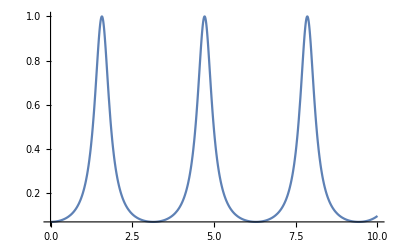

```mathematica
Plot[1/Ti/.{k->1,κ->1,a->1},{b,0,10},PlotRange->All]
```